```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"code","2D","out","poiseuille"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/poiseuille

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
myPlot[val_,labels_, drop_]:=ListLinePlot[Drop[val,drop], PlotLegends->Drop[labels,drop], PlotRange->All];
myPlotFromTo[val_,labels_, from_, to_]:=ListLinePlot[Part[val,from;;to], PlotLegends->Part[labels,from;;to], PlotRange->All];
getLengths[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,6] &/@StringCases[thelist, RegularExpression["length([0-9]*)"]]] ;
```

```mathematica
inlet ={0.0,0.00387812,0.01096953,0.01717452,0.02249307,0.02692521,0.03047091,0.03313019,0.03490305,0.03578947,0.03578947,0.03490305,0.03313019,0.03047091,0.02692521,0.02249307,0.01717452,0.01096953,0.00387812,0.0};
```

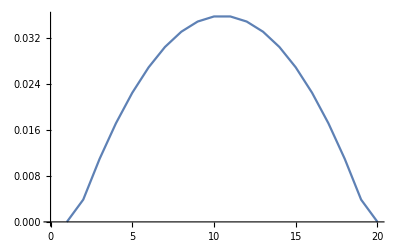

```mathematica
ListLinePlot[inlet]
```

```mathematica
lengthsSrt = getLengths[srts];
permutationSrt = Ordering[lengthsSrt];
valuesSrt = Flatten /@ Import /@ srts[[permutationSrt]];
labelsSrt = lengthsSrt[[permutationSrt]];
errorSrt = (Abs[# -inlet]) &/@ valuesSrt;
```

```mathematica
lengthsSrt[[permutationSrt]]
```

{3,5,7,9,11,15,20,25,30,35,40,45,50,60,70,80,90,100}

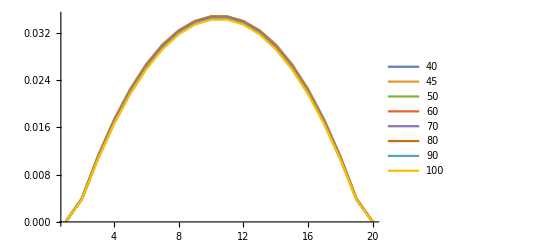

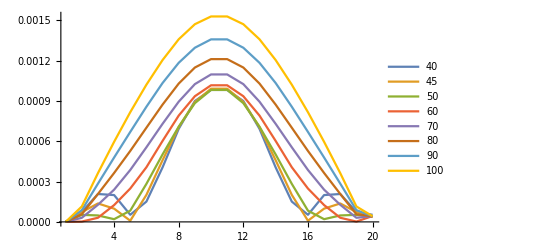

```mathematica
myPlot[valuesSrt,labelsSrt,10]
myPlot[errorSrt,labelsSrt,10]
```

```mathematica
lengthsCumulant = getLengths[cumulants];
permutationCumulant = Ordering[lengthsCumulant];
valuesCumulant = Flatten /@ Import /@ cumulants[[permutationCumulant]];
labelsCumulant = lengthsCumulant[[permutationCumulant]];
errorCumulant = (Abs[# -inlet]) &/@ valuesCumulant;
```

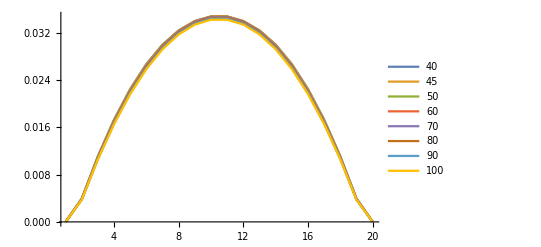

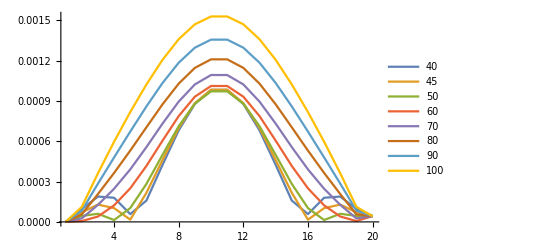

```mathematica
myPlot[valuesCumulant,labelsCumulant,10]
myPlot[errorCumulant,labelsCumulant,10]
```

```mathematica
cumulantVsSrtError = errorCumulant-errorSrt;
cumulantVsSrtErrorTotal = Total /@ cumulantVsSrtError;
```

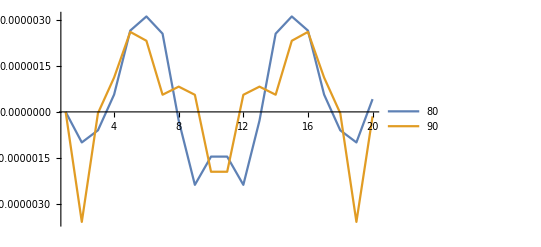

```mathematica
myPlotFromTo[cumulantVsSrtError,labelsSrt,16,17]
```

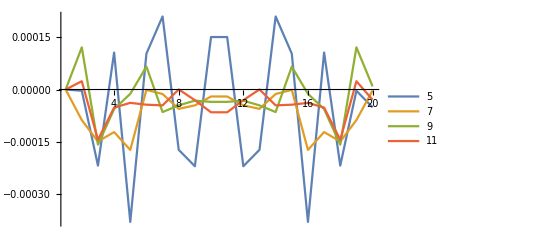

```mathematica
myPlotFromTo[cumulantVsSrtError,labelsSrt,2,5]
```

```mathematica
labelsSrt
```

{3,5,7,9,11,15,20,25,30,35,40,45,50,60,70,80,90,100}

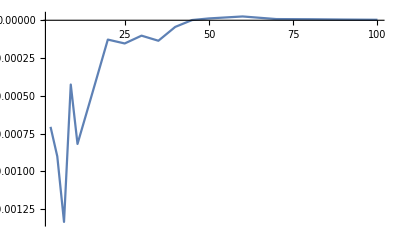

```mathematica
ListLinePlot[Transpose[{labelsSrt,cumulantVsSrtErrorTotal}], PlotRange->All]
```

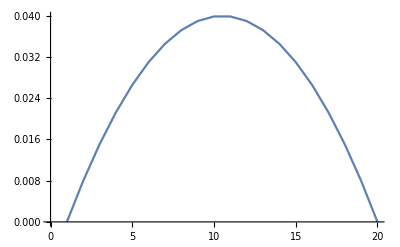
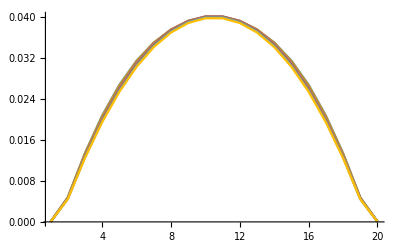
```mathematica
Show[-Graphics-,-Graphics-]
```

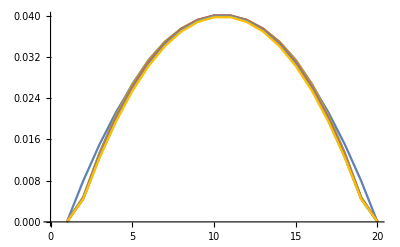

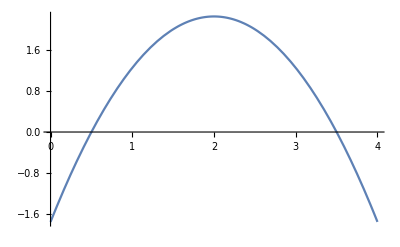

```mathematica
Plot[(x-0.5)*(4-x-0.5),{x,0,4}]
```